This notebook shows cavity optomechanical calculations using the method outlined in the paper “Exact steady state of perturbed open quantum systems”: https://arxiv.org/abs/2501.06134. See the paper for detailed explanation of the technique. 

If you use this work for research, we would appreciate citing the paper.

- Omar Nagib* and Thad G. Walker**

*onagib@wisc.edu
**tgwalker@wisc.edu

************************************************************************************

Notational definitions

vectorization:  want to represent the N×N density matrix as a N^2 column vector

let v(A)=|A)=∑_ij A_ij i⊗j=∑_ij A_ij i j
Example:  two-level atom ρ=ρ_ee | ρ_eg
ρ_ge | ρ_gg->v(ρ)=ρ_ee
ρ_eg
ρ_ge
ρ_gg

```mathematica
<<Notation`
```

```mathematica
v[A_]:=Flatten[A]
```

Define ⊗ as Kronecker product of x and y:

```mathematica
ClearAll[CircleTimes];

CircleTimes[x_,y_]:=KroneckerProduct[x,y];
```

Define the symbol 𝕀_n as the n by n Identity matrix:

```mathematica
ClearAll[𝕀];
Subscript[𝕀,n_]:=IdentityMatrix[n];
```

Define ᵀ as transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"ᵀ"]]⟹ParsedBoxWrapper[RowBox[{"Transpose","[",x,"]"}]]];
```

Define † as conjugate transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"†"]]⟹ParsedBoxWrapper[RowBox[{"ConjugateTranspose","[",x,"]"}]]];
```

Define | ⟩ as a column vector, a ket:

```mathematica
ClearAll[Ket];

Ket[v_List]:=Transpose[{Flatten[v]}];
```

Define * as conjugate transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"*"]]⟹ParsedBoxWrapper[RowBox[{"Conjugate","[",x,"]"}]]];
```

************************************************************************************
Steady state phonon number (by sampling):

In cavity optomechanics, we have an optical cavity coupled to a mechanical oscillator with the Hamiltonian:

H=  -Δ a^†a+ω_m b^†b-g(b^†+b)a^†a+η(a+a^†)

where a_ and b is are the annihilation operators of the cavity and the oscillator, respectively. ω_m is the mechanical oscillator frequency, Δ_=ω_L-ω_c is the detuning between the pump laser and the cavity resonance frequency. g is the interaction strength between the cavity and the oscillator. η is the laser pump strength. A laser with detuning Δ_=-ω_m leads to mechanical cooling of the oscillator (low phonon number at steady state) via the cavity-optomechanical interaction. For photon loss, we have the Lindblad operator:

 L=√κ a (destroying a cavity photon at a decay rate κ). 
 
The total state would be the tensor product of the mechanical oscillator and the cavity in the Fock basis |n>_m ⊗ |l>_c (|n>_m denotes n phonons for the mechanical oscillator and |l>_c denotes l photons in the cavity). A phonon-photon Fock state is given by:
  
  |ψ> =∑_(n,l) ψ_(n ,l) |n>_m ⊗ |l>_c 
  
  More generally, the density matrix of the composite system is:
  
  ρ = ∑_(n ,n', l, l') ρ_(n ,n', l, l') |n>_m<n'|_m ⊗ |l>_c<l'|_c 
  
  While the vectorized density matrix would be:
  
    ρ = ∑_(n ,n', l, l') ρ_(n ,n', l, l') (|n>_m|n'>_m) ⊗ (|l>_c|l'>_c) 
    
If the steady state is given by ρ_∞, then the average photon number at steady state is <n_m> =Tr(b^†b ρ_∞) then using the identity

 (v(B))^†.v(A)=B_ij^*A_kl(i⊗j).(k⊗l)=B_ij^*A_ij=Tr[B^† A] 
 
 we get
 
 <n_m> =v(b^†b).v(ρ_∞)=(v(b^†b))^†.ρ_∞
 
 Similarly, for the steady-state cavity photon number:
 
 <n_c> =v(a^†a).v(ρ_∞)=(v(a^†a))^†.ρ_∞

First, let’s construct our operators.

Use the identity: a|n> =√n|n-1> and a^†|n> = √(n+1)|n+1> so

<m|a|n> =√n δ_(m,n-1) and <m|a^†|n> =√(n+1)δ_(m,n+1) 

The  calculations below and the parameters are inspired from this Julia notebook:
  
  https://docs.qojulia.org/examples/optomech-cooling/#Optomechanical-Cavity

```mathematica
Nm=4;(*Fock space dimension for mechanical oscillator, with operator b*)
```

```mathematica
Nc=1;(*Fock space dimension for cavity, with operator a*)
```

```mathematica
aminus=SparseArray[1.Table[Sqrt[j]KroneckerDelta[i,j-1],{i,0,Nc},{j,0,Nc}]];
```

```mathematica
bminus=SparseArray[1.Table[Sqrt[j]KroneckerDelta[i,j-1],{i,0,Nm},{j,0,Nm}]];
```

The a_ and b operators are actually given by: b_=b_m ⊗ I_c and a=I_m ⊗ a_c:

```mathematica
b=bminus⊗Subscript[𝕀, Nc+1];
```

```mathematica
a=Subscript[𝕀, Nm+1]⊗aminus;
```

Define  the system parameters:

```mathematica
Δ=-10.;
ω=10;
g=1.;
η=2.;
κ=1.;
Γ=0.015;
navg=2;
```

We  can write our Hamiltonian as: H= - Δ a^†a+ω_m b^†b-g_0(b^†+b)a^†a+η(a+a^†) as

```mathematica
H=-Δ SuperDagger[a].a+ω SuperDagger[b].b-g(SuperDagger[b]+b).(SuperDagger[a].a)+η (SuperDagger[a]+a);
```

Define the Lindblad operator:

```mathematica
L=√κ a;
```

Moreover, let’s couple the mechanical oscillator to a thermal bath with Lindblad operators:

J_out=√(Γ(n_avg+1))b, J_in=√(Γ n_avg)b^†,

```mathematica
Jout=√(Γ(navg+1))b;
```

```mathematica
Jin=√(Γ navg)SuperDagger[b];
```

Construct the Lindbladian for the total system:

```mathematica
ℒ=-I(H⊗Subscript[𝕀, Length[H]]-Subscript[𝕀, Length[H]]⊗Hᵀ)+( L⊗L-1/2 Lᵀ.L⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗Lᵀ.L)+( Jin⊗Jin-1/2 Jinᵀ.Jin⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗Jinᵀ.Jin)+ ( Jout⊗Jout-1/2 Joutᵀ.Jout⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗Joutᵀ.Jout);
```

The steady state of the system is given by ℒ ρ =0, where ρ denotes the state of the photons and the phonons . Find the nullspace then renormalize by dividing by the trace. We use the “Shift-and-invert” Arnoldi/Krylov method with shift=0, which means find the eigenvector whose eigenvalue is closest to zero (i.e., the nullspace right vector):

```mathematica
ρnullspace=Flatten[Eigenvectors[ℒ,1,Method->{"Arnoldi","Shift"->0}]];Traceρnullspace=v[Subscript[𝕀, Length[H]]].ρnullspace;
ρ∞=ρnullspace/Traceρnullspace;
```

Let’s find average phonon number <n_m>:

```mathematica
nm=v[SuperDagger[b].b].ρ∞//Chop
```

0.485727

Let’s find  average cavity photon number<n_c>:

```mathematica
nc=v[SuperDagger[a].a].ρ∞//Chop
```

0.0611688

Next, we create a module ρΔsampleSparse that computes the steady state for any Δ by initializing a new Lindbladian for every Δ, and find its nullspace. Here, The new solution is built on top of ℒ as ℒ+Δ ℒ_1 where H_1=-a^†a. So we find the steady state of ℒ+Δ ℒ_1. The steady state is normalized as well.

First  construct ℒ_1 from H_1.

```mathematica
H1=-SuperDagger[a].a;
```

```mathematica
ℒ1=-I(H1⊗Subscript[𝕀, Length[H]]-Subscript[𝕀, Length[H]]⊗H1ᵀ);
```

```mathematica
VecI=v[Subscript[𝕀, Length[H]]];
```

```mathematica
ρΔsampleSparse[Δ0_]:=Module[{Δ0temp=Δ0,ℒtest0,ρnullspacetest,Traceρnullspacetest,ρ∞test},ℒtest0=ℒ+Δ0temp ℒ1;ρnullspacetest=Flatten[Eigenvectors[ℒtest0,1,Method->{"Arnoldi","Shift"->0}]];Traceρnullspacetest=VecI.ρnullspacetest;
ρ∞test=ρnullspacetest/Traceρnullspacetest]
```

************************************************************************************
Steady state phonon number by the present method:
See the paper for details of the theory and the numerical implementation.

We would like to find the steady state as a function of .  First, construct  ℒ_0^-. Then we construct ℒ_1 from H_1, where H_1=-a^†a. So our total Lindbladian is  ℒ_0 +Δℒ_1. Then we diagonalize ℒ_0^-ℒ_1 to construct its right and left eigenvectors r_λ and l_λ and their eigenvalues λ. So that our final solution becomes:

ρ_Δ=(∑_λ 1/(1+λ Δ)r_λ⊗l_λ)ρ_0

To construct ℒ_0^-: we describe two methods. 

Method 1) Diagonalization method:

we diagonalize it to find the right and left eigenvectors R_g and L_g and their eigenvalues g. We construct the left eigenvectors by taking the inverse of the transpose of the right eigenvector matrix. Note that PseudoInverse and Inverse are the same operations, ideally, for invertible matrices, which is the case here. ℒ_0^- is the inverse of ℒ_0 excluding the zero eigenvectors and eigenvalues:

ℒ_0^-=∑_(g≠0) 1/g R_g⊗(L^T)_g

```mathematica
(*{egnv,Regnvec}=Eigensystem[ℒ0];*)
```

```mathematica
(*Legnvec=PseudoInverse[Transpose[Regnvec]];*)(*The Moore-Penrsoe inverse, dubbed PseudoInverse in Mathematica, and the Inverse are the same for invertible matrices*)
```

To construct ℒ_0^-, we denote R_-=(R_1 R_2...R_(N-1)), where R_g is the column right eigenvector with length N, and L_-=(L_1 L_2...L_(N-1)), where L_g is the column left eigenvector with length N. Let G_-=(g_1 g_2... g_(N-1)) be the list of eigenvalues. The minus subscript in R_-, L_-, and G_- denotes that we are excluding the zero eigenvalues and vectors from these objects.  An equivalent way to rewrite ℒ_0^- is then

ℒ_0^-=(1/(G_-)R_- ).(L_-)^T (normal version)

Here 1/(G_-)R_- denotes the elementwise division: (R_1/g_1 R_2/g_2...(R_(N-1))/(g_(N-1))) while the dot denotes normal matrix multiplication. In Mathematica, the output of eigensystem are rows not columns. Therefore, in Mathematica it is be given by

ℒ_0^-=(1/(G_-)R_- )^T.L_-   (Mathematica version)

```mathematica
(*ℒ0minus=Transpose[(1/egnv[[1;;-2]])Regnvec[[1;;-2,All]]].Legnvec[[1;;-2,All]];*)
```

where the 1;;-2 gets all the rows (eigenvectors) except the last one, which is the zero eigenvector/eigenvalue.

Method 2) Using an inverse identity:

We note that ℒ_0^- can be directly constructed as

ℒ_0^-=(ℒ_0+ (R_0 L_0^T))^-1-R_0 L_0^T

i.e., add the nullspace projector P_0=R_0 L_0^T, take the inverse, and then subtract P_0 again. This completely avoids explicit diagonalization and construction of right/left eigenvectors.

```mathematica
P0=SparseArray[KroneckerProduct[ρ∞,Transpose[v[Subscript[𝕀, Length[H]]]]]];
```

```mathematica
(*xsucc=LinearSolve[ℒSparse0,SparseP0];*)
```

```mathematica
ℒ0minus=Inverse[ℒ+P0]-P0;
```

Next, we diagonalize ℒ_0^-ℒ_1 to find the right and left eigenvectors r_λ, l_λ and the eigenvalues λ.

```mathematica
{λ,rλ}=Eigensystem[ℒ0minus.ℒ1];
```

```mathematica
Lλ=Inverse[Transpose[rλ]];(*The Moore-Penrsoe inverse, dubbed PseudoInverse in Mathematica, and the Inverse are the same for invertible matrices*)
```

Then the exact perturbed steady state for any Δ is:

ρ_Δ=(∑_λ 1/(1+λ Δ)r_λ⊗l_λ)ρ_0 can be rewritten compactly and efficiently as 

ρ_Δ={(1/(1+Δ Λ)r)^T.l}.ρ_0 

where r=(r_1 r_2...r_N) is the right eigenvectors of ℒ_0^-.ℒ_1 and l=(l_1 l_2...l_N) are the left eigenvectors and Λ=(λ_1 λ_2... λ_N) are the eigenvalues. 1/(1+Δ Λ)r is an elementwise division between Λ and r while the dot denotes matrix multiplication:

If we work in the eigenbasis of ℒ_0^-.ℒ_1, then every original vector (vectorized density matrix or an operator) gets mapped into ρ-->l^T.ρ in the new basis. Row vectors in the conjugate space gets mapped into (vec(A))^†-->(vec(A))^†.r . Note that r=l^-1. In this eigenbasis,  updating ρ_Δ for a new Δ merely amounts to updated 1/(1+Δ λ_i) for N different λ_i. 

Note that in Mathematica’s convention the mapping would actually be:

 ρ-->l.ρ
 (vec(A))^†-->(vec(A))^†.r^T

```mathematica
lλρ∞=Lλ.ρ∞;(*The unperturbed steady state in the new eigenbasis*)
```

```mathematica
ρΔ[Δ_]:=(1/(1+Δ λ) lλρ∞);(*The perturbed steady state in the new eigenbasis*)
```

```mathematica
rλT=Transpose[rλ];
```

Map the vectorized phonon number operator into the new eigenbasis:

```mathematica
vbb=v[SuperDagger[b].b];
```

```mathematica
vbbnew=v[SuperDagger[b].b].rλT;
```

Combining all the above, the perturbed phonon steady state is:

```mathematica
vbρΔ[Δ_]:=vbbnew.ρΔ[Δ];
```

We can gain additional speed by excluding all the zero eigenvalues of  ℒ_0^-.ℒ_1:

Using the identity 1/(I+A)=I-A/(1+A) on ρ_Δ. We get 

ρ_Δ=ρ_0-{((Δ Λ)/(1+Δ Λ)r)^T.l}.ρ_0

Note that we can exclude all the nullspaces/zero eigenvectors/values in the second term, without affecting ρ_Δ. 

In the present case under study, the non-zero eigenvalues run from 1 to r, where r is the rank of ℒ_1; the rest are zero (see below).

```mathematica
r=MatrixRank[ℒ1]
```

50

```mathematica
λ[[r]]
λ[[r+1]]
```

-0.0199214-0.000242881 ⅈ

0.

```mathematica
lλρ∞nnz=Lλ[[1;;r]].ρ∞;
rλTnnz=Transpose[rλ[[1;;r]]];
λnnz=λ[[1;;r]];
```

Since  we are interested in the expectation value, then we can evaluate the dot product between the vectorized phonon number operator and the vectorized density matrix in that new basis as follows:

```mathematica
vbbnnz=v[SuperDagger[b].b].rλTnnz;
```

Precompute the unperturbed steady state phonon number:

```mathematica
nb∞=v[SuperDagger[b].b].ρ∞;
```

Precompute the vectorized phonon number operator operator (only acting on the nonzero eigenvalues)

```mathematica
vbbnnz=v[SuperDagger[b].b].rλTnnz;
```

Therefore, combining all the above, we finally get the perturbed steady state phonon number:

```mathematica
vbρΔnnz[Δ_]:=nb∞-vbbnnz.(lλρ∞nnz(Δ λnnz)/(1+Δ λnnz));
```

************************************************************************************

Generate a table average phonon number vs Δ/ω_m, where ω_m=10 here. We want the plot to be around Δ/ω_m=-1 or Δ=-10. Note that ρΔ[Δ=0] gives the steady state at Δ=-10, and so on. Using the two definitions:

```mathematica
testTable=Table[{Δ/10-1,Re[vbρΔ[Δ]]},{Δ,-8,4,0.1}];
```

```mathematica
testTable2=Table[{Δ/10-1,Re[vbρΔnnz[Δ]]},{Δ,-8,4,0.1}];
```

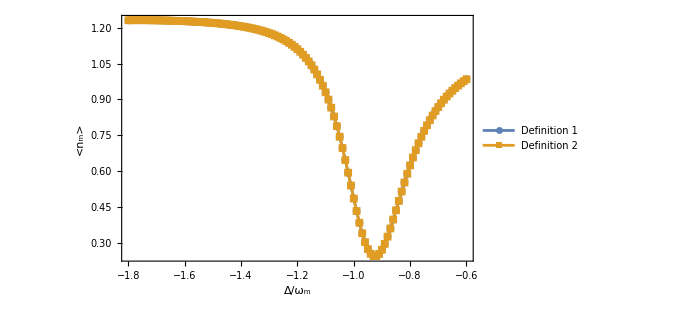

```mathematica
ListPlot[{testTable,testTable2},FrameLabel->{"Δ/ω_m","<n_m>"},Frame->True,FrameStyle->Directive[GrayLevel[0],17,FontFamily->"Helvetica",AbsoluteThickness[1.0]],GridLines->None,ImageSize->500,PlotRange->All,Axes->False,Joined->True,InterpolationOrder->2,PlotMarkers->{Automatic,8},PlotLegends->Placed[LineLegend[{"Definition 1","Definition 2"}],{0.7,0.8}]]
```

************************************************************************************
Comparing accuracy: present approach vs repeatedly solving for the nullspace (using Arnoldi): 

i.e., comparing vbρΔ and ρΔsampleSparse.

```mathematica
testTableSample=Table[{Δ/10-1,Re[vbb.ρΔsampleSparse[Δ]]},{Δ,-8,4,0.1}];
```

Compare the present approach with numerically sampling+finding the nullspace:

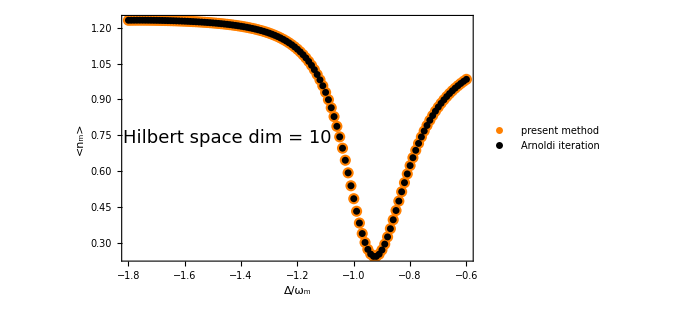

```mathematica
ListPlot[{testTable,testTableSample},FrameLabel->{"Δ/ω_m","<n_m>"},Frame->True,FrameStyle->Directive[GrayLevel[0],20,FontFamily->"Helvetica",AbsoluteThickness[1.0]],GridLines->None,ImageSize->500,PlotRange->All,Axes->False,Joined->{False,False},InterpolationOrder->2,PlotStyle->{Directive[Orange,AbsolutePointSize[8]],Directive[Black,AbsolutePointSize[5],Style["■"]]},PlotLegends->Placed[LineLegend[{"present method","Arnoldi iteration",""},LegendMarkerSize->{20,10}],{0.3,0.15}],LabelStyle->{FontSize->20,FontFamily->"Helvetica"},Epilog->{Text[Style["Hilbert space dim = 10",18],Scaled[{0.3,0.5}]   ]}]
```

************************************************************************************
Comparing Timing: present approach vs repeatedly solving for the nullspace (using Arnoldi) for different number of samples P:

For the present approach, we have to take into account the constant overhead time taken in constructing the Drazin inverse ℒ_0^- (which also requires finding the nullspace ρ_0) as well as diagonalizing ℒ_0^-ℒ_1. For a fair comparison, we also find ρ_0 using the Arnoldi iteration.

```mathematica
ConstOverheadTime=Timing[ρnullspace=Flatten[Eigenvectors[ℒ,1,Method->{"Arnoldi","Shift"->0}]];Traceρnullspace=v[Subscript[𝕀, Length[H]]].ρnullspace;
ρ∞=ρnullspace/Traceρnullspace;P0=SparseArray[KroneckerProduct[ρ∞,Transpose[v[Subscript[𝕀, Length[H]]]]]];
(*xsucc=LinearSolve[ℒSparse0,SparseP0];*)ℒ0minus=Inverse[ℒ+P0]-P0;{λ,rλ}=Eigensystem[ℒ0minus.ℒ1];
Lλ=Inverse[Transpose[rλ]];nb∞=v[SuperDagger[b].b].ρ∞;vbbnnz=v[SuperDagger[b].b].rλTnnz;][[1]]
```

0.013048

Now, let’s compile a table which computes the CPU time in generating the steady state as (P,CPU time) for both approaches, and see at which P, the present approach becomes more favorable?

Present approach 1: Measure CPU time using timing

```mathematica
(*1. List of P values*)PList={1,10,10^2,10^3,10^4,10^5};

(*2. Δ-range—adjust as needed*)
{Δmin,Δmax}={−5,+5};

(*3. Build the table {P,CPU time}*)
Block[{$HistoryLength=0},timingTable1=Table[cpu=First@Timing[Module[{i},(*loop P times,computing ρΔ2 at each sample but not storing it*)Do[v[SuperDagger[b].b].vbρΔnnz[If[P==1,Δmin,(*when P=1 just use one point*)Δmin+(i-1)*(Δmax-Δmin)/(P-1)  (*evenly spaced grid*)]];,{i,1,P}](*clear any cached factorizations once,after the batch*)ClearSystemCache[];]];
{P,cpu},{P,PList}];]

(*4. Display as a table*)
TableForm[timingTable1,TableHeadings->{None,{"P","CPU time (s)"}}]
```

P | CPU time (s)
1 | 0.001366
10 | 0.00091
100 | 0.005943
1000 | 0.0452
10000 | 0.383442
100000 | 3.78143

```mathematica
timingTable1
```

{{1,0.001366},{10,0.00091},{100,0.005943},{1000,0.0452},{10000,0.383442},{100000,3.78143}}

Present approach 2: Measure CPU time using TimeUsed[]

```mathematica
(*1. Your P list and Δ-range*)PList={1,10,10^2,10^3,10^4,10^5};
{Δmin,Δmax}={-5,+5};

Block[{$HistoryLength=0},(*never store Out[n]*)timingTable2=Table[Module[{start,finish},(*record CPU time before doing any work*)start=TimeUsed[];
(*do P calls,but do NOT store their results*)Do[v[SuperDagger[b].b].vbρΔnnz[If[P==1,Δmin,Δmin+(i-1)*(Δmax-Δmin)/(P-1)]],{i,1,P}];
(*clear any cached factorizations once,after the batch*)ClearSystemCache[];
(*record CPU time after the loop*)finish=TimeUsed[];
(*output {P,total CPU seconds}*){P,finish-start}],{P,PList}];];

(*finally,display it*)
TableForm[timingTable2,TableHeadings->{None,{"P","CPU time (s)"}}]
```

P | CPU time (s)
1 | 0.00048
10 | 0.000832
100 | 0.006226
1000 | 0.045997
10000 | 0.372281
100000 | 3.71761

```mathematica
timingTable2
```

{{1,0.00048},{10,0.000832},{100,0.006226},{1000,0.045997},{10000,0.372281},{100000,3.71761}}

Now  add the constant overhead time to this time to compute the total CPU time for generating P samples:

```mathematica
(*Method C:Map over rows*)timingTableAdjusted={#[[1]],#[[2]]+ConstOverheadTime}&/@timingTable2
```

{{1,0.013528},{10,0.01388},{100,0.019274},{1000,0.059045},{10000,0.385329},{100000,3.73066}}

Arnoldi approach 1: Measure CPU time using timing

```mathematica
(*1. List of P values*)PList={1,10,10^2,10^3,10^4,10^5};

(*2. Δ-range—adjust as needed*)
{Δmin,Δmax}={−5,+5};

(*3. Build the table {P,CPU time}*)
Block[{$HistoryLength=0},timingTableArnoldi1=Table[cpu=First@Timing[Module[{i},(*loop P times,computing ρΔ2 at each sample but not storing it*)Do[vbb.ρΔsampleSparse[If[P==1,Δmin,(*when P=1 just use one point*)Δmin+(i-1)*(Δmax-Δmin)/(P-1)  (*evenly spaced grid*)]];,{i,1,P}](*clear any cached factorizations once,after the batch*)ClearSystemCache[];]];
{P,cpu},{P,PList}];]

(*4. Display as a table*)
TableForm[timingTableArnoldi1,TableHeadings->{None,{"P","CPU time (s)"}}]
```

P | CPU time (s)
1 | 0.001513
10 | 0.007209
100 | 0.048671
1000 | 0.39534
10000 | 4.01906
100000 | 41.5182

```mathematica
timingTableArnoldi1
```

{{1,0.001513},{10,0.007209},{100,0.048671},{1000,0.39534},{10000,4.01906},{100000,41.5182}}

Arnoldi approach: Implementation style 2

```mathematica
(*1. Your P list and Δ-range*)PList={1,10,10^2,10^3,10^4,10^5};
{Δmin,Δmax}={-5.,+5.};

Block[{$HistoryLength=0},(*never store Out[n]*)timingTableArnoldi2=Table[Module[{start,finish},(*record CPU time before doing any work*)start=TimeUsed[];
(*do P calls,but do NOT store their results*)Do[vbb.ρΔsampleSparse[If[P==1,Δmin,Δmin+(i-1.)*(Δmax-Δmin)/(P-1.)]],{i,1,P}];
(*clear any cached factorizations once,after the batch*)ClearSystemCache[];
(*record CPU time after the loop*)finish=TimeUsed[];
(*output {P,total CPU seconds}*){P,finish-start}],{P,PList}];];

(*finally,display it*)
TableForm[timingTableArnoldi2,TableHeadings->{None,{"P","CPU time (s)"}}]
```

P | CPU time (s)
1 | 0.001608
10 | 0.006937
100 | 0.049241
1000 | 0.41291
10000 | 4.18901
100000 | 42.0067

```mathematica
timingTableArnoldi2
```

{{1,0.001608},{10,0.006937},{100,0.049241},{1000,0.41291},{10000,4.18901},{100000,42.0067}}

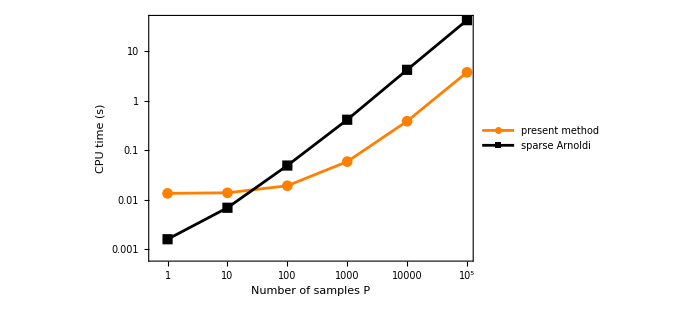

```mathematica
ListLogLogPlot[{timingTableAdjusted,timingTableArnoldi2},FrameLabel->{"Number of samples P","CPU time (s)"},Frame->True,FrameStyle->Directive[GrayLevel[0],20,FontFamily->"Helvetica",AbsoluteThickness[1.0]],GridLines->None,ImageSize->500,PlotRange->All,Axes->False,Joined->True,PlotMarkers->Automatic,PlotStyle->{Directive[Orange,AbsolutePointSize[8]],Directive[Black,AbsolutePointSize[5],Style["■"]]},PlotLegends->Placed[LineLegend[{"present method","sparse Arnoldi",""},LegendMarkerSize->{20,10}],{0.72,0.15}],LabelStyle->{FontSize->20,FontFamily->"Helvetica"}]
```